```mathematica
data1=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\problem\\1.txt",{Number,Number}];
data2= ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\problem\\2.txt",{Number,Number}];
data= ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\problem\\newXY.txt",{Number,Number}];
```

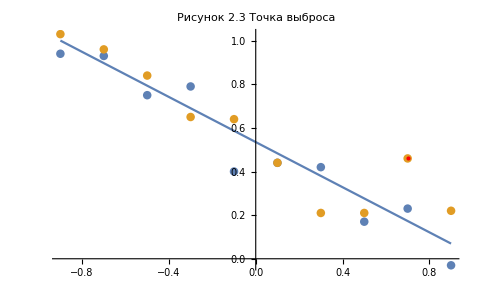

```mathematica
lp=ListPlot[{data1,data2},PlotRange->All, PlotLabel->"Рисунок 2.3 Точка выброса"];
llp=ListLinePlot[data,PlotRange->All];
Show[lp, llp,Graphics[{PointSize[Medium],Red,Point[{0.7,0.46}]}]]
```